```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

## Setup

```mathematica
(*ResourceFunction["matexInstall"][];
*)
(* Needs["PacletManager`"];
PacletInstall["C:\\Users\\jonat\\Downloads\\matex-1.7.10.paclet"];
Configurematex[
"pdfLaTeX"->"C:\\texlive\\2023\\bin\\windows\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.04.0\\bin\\gswin64c.exe"
] *)

(*<< matex`
SetOptions[matex,"Preamble"->{"\\usepackage{CormorantGaramond,gillius2}"}];
*)
pvectorName[n_] := Subscript[p, n]
phatvectorName[n_] := Subscript[OverHat[p], n];
paraNumber[n_] := paraNumber[n,0.03];
paraNumber[n_,scale_] := Style[ToString[n],FontFamily->jStyle["FontFamily"],FontSize->Scaled[scale]];
paraGillNumber[n_,scale_] := Style[ToString[n],FontFamily->jStyle["DisplayFontFamily"],FontSize->Scaled[scale]];

jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->jStyle["FontFamily"],FontSize->n};
```

```mathematica
exportFigures := Timing@{
txbExport[Txb0403Coordinates]
,txbExport[Txb0404Complementary]
,txbExport[Txb0405Parastichy5]
,txbExport[Txb0406Parastichy45]
,txbExport[Txb0407PPairs]
,txbExport[Txb0408Periodic]
,txbExport[Txb0409Apextriangle]
,txbExport@Txb0410GeneratingIntervals,
,txbExport[Txb0411LatticesSpecialD]
,txbExport[Txb0412Spiral ]
,txbExport@Txb0413SpiralExample
,txbExport[Txb0414Reduction]
,txbExport[Txb0415SumDifference]
,txbExport[Txb0416FibLattices]
,txbExport[Txb0417LatticeTypes]
, txbExport[Txb0418LowOrder]
, txbExport[Txb0419JeanX]
};
shExport[x_] := x;
```

```mathematica
(* not currently used buy maybe should be *)
{
txbExport[Txb0400duBonnet]

};
```

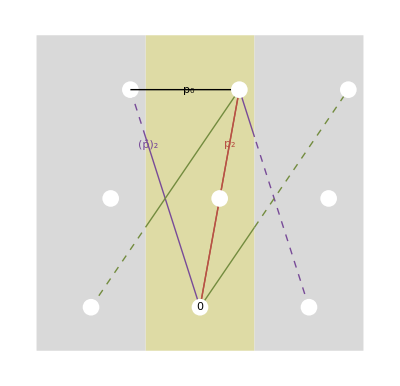
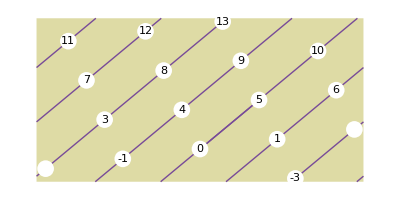
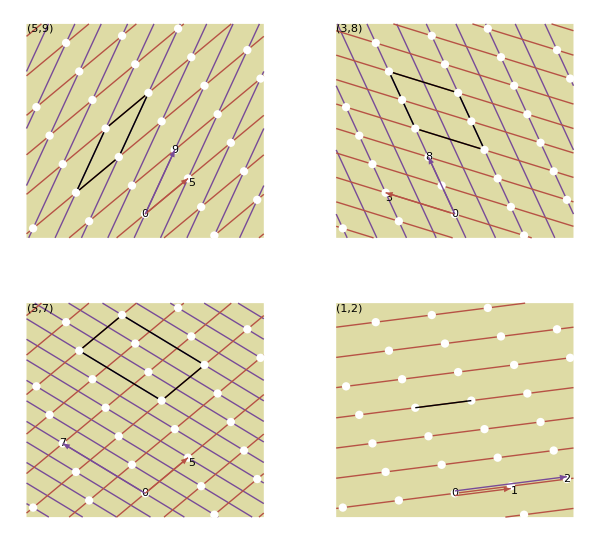
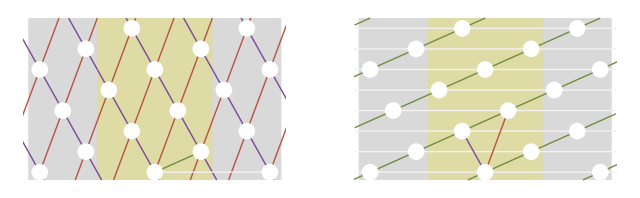
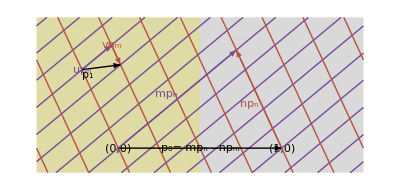
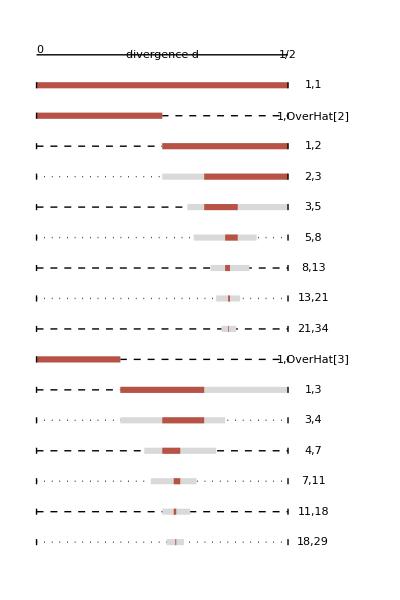
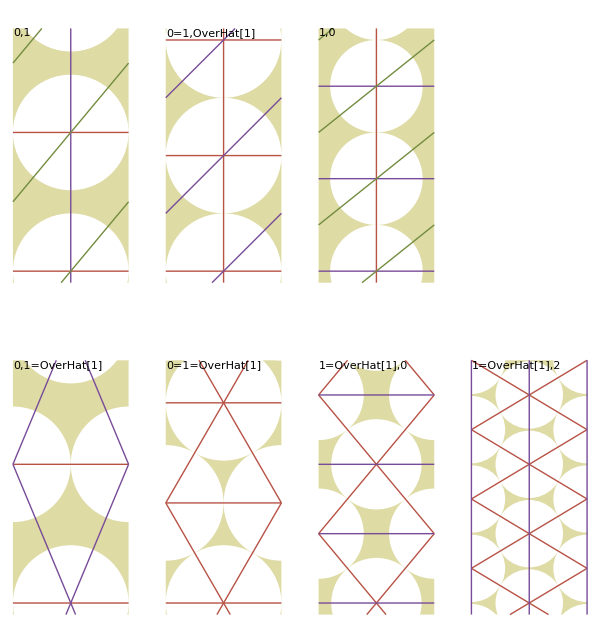
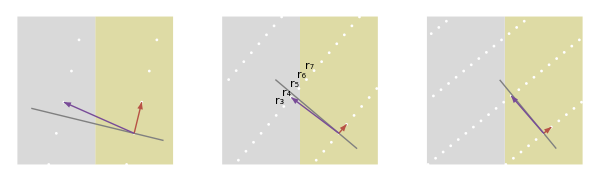
{0.546875,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
exportFigures
```

## Txb0401 Leaftypes

```mathematica
leafRose = Import["Data\\LeafMesh.mx"];
l1 = TransformedRegion[leafRose,ReflectionTransform[{0,1,0}]@* TranslationTransform[{-2604,-1814,0}]];
```

```mathematica
l2 =TransformedRegion[l1,ReflectionTransform[{1,0,0}]@*ReflectionTransform[{0,1,0}]];
```

```mathematica
l12 = RegionUnion[l1,l2];
```

```mathematica
l123= RegionUnion[l1
,TransformedRegion[l1,RotationTransform[ 120 Degree,{0,0,1}]]
,TransformedRegion[l1,RotationTransform[ 240 Degree,{0,0,1}]]
];

gLeaf[{height_,rotation_}] := MeshPrimitives[#,2]& @TransformedRegion[l1,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];

gLeafPair[{height_,rotation_}] := MeshPrimitives[#,2]& @TransformedRegion[l12,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];

gWhorl[{height_,rotation_}] := MeshPrimitives[#,2]& @
TransformedRegion[l123,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];
```

```mathematica
spiral:= Module[{pairTable},
pairTable= Table[gLeaf[ {100 *n,20  Degree+GoldenAngle * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
alternateDistichous:= Module[{pairTable},
pairTable= Table[gLeaf[ {100 *n,-20  Degree+180 Degree * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
oppositeDistichous := Module[{pairTable},
pairTable= Table[gLeafPair[ {100+200 *n,-20 Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
```

```mathematica
mLeafPair[{height_,rotation_}] := TransformedRegion[l12,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];
```

```mathematica
(*pairTable= Table[gLeafPair[ {100+200 *n,-20 Degree}],{n,0,2}]*)
```

```mathematica
oppositeDecussate := Module[{pairTable},
pairTable= Table[gLeafPair[ {100+200 *n,-20 + n  90Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
whorled := Module[{pairTable},
pairTable= Table[gWhorl[ {100+200 *n,-20 + n  90Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
decussate := Module[{pairTable},
pairTable= Table[gLeafPair[ {100 *n,90 Degree * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,500}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
```

```mathematica
Ch3Types := Module[{},
 types ={
<|"label"->"Spiral","graphics"->spiral,"jugacy"->1,
"lattice"->spiralLattice,"class"-> "(0,1)"|>
,<|"label"->"Alternate\ndistichous","graphics"->alternateDistichous,"jugacy"->1,
"lattice"->alternateDistichousLattice,"class"-> "(0,1=1)"|>
,<|"label"->"Opposite\ndistichous","graphics"->oppositeDistichous,"jugacy"->2,
"lattice"->oppositeDistichousLattice,"class"-> "2x(0,1,1)"|>
,<|"label"->"Decussate","graphics"->oppositeDecussate,"jugacy"->2,
"lattice"->oppositeDecussateLattice,"class"-> "2x(0,1=1)"|>
,<|"label"->"Whorled","graphics"->whorled,"jugacy"->3,
"lattice"->whorledLattice,"class"-> "3x(0,1,1)"|>
};
boxsize= 50;raster[g_] := Rasterize[#,ImageResolution->300,ImageSize->72]& @ Show[Graphics3D[{Opacity[0.],EdgeForm[None],Cuboid[{-boxsize,-boxsize,0},{boxsize,boxsize,520}]}],g,Boxed->False];

rtypes = Map[Append[#,"raster"->raster[#["graphics"]]]&,types];
data = Map[  {Item[#["raster"],ItemSize->Automatic]
,Item[Style[#["label"],jFont[12]],ItemSize->All]
,("J="<> ToString[#["jugacy"]] )
, Style[#["class"],jFont[12]]
, #["lattice"]
}&,rtypes];
Grid[Transpose[data]]
];
```

```mathematica
spiralLattice := Module[{},lattice= latticeCreateDH[{1/GoldenRatio^2,1},{-0.1,5.1}];
jpt[m_] := latticePoint[lattice,m];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
alternateDistichousLattice := Module[{},lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
jpt[m_] := latticePoint[lattice,m];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]-{1,0}}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
decussateLattice := Module[{},
lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
lpts=Point[{{-1/8,0},{3/8,0},{-3/8,2},{1/8,2},{-1/8,4},{3/8,4}}];
g = Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{PointSize[0.06],White,lpts}
,{Thick,jParastichyColour[1],Arrow[{{-1/8,0},{-3/8,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{-1/8,0},{1/8,2}}]}

},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
oppositeDistichousLattice := Module[{},
lpts=Point[{{-1/8,0},{3/8,0},{-1/8,2},{3/8,2},{-1/8,4},{3/8,4}}];
g = Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{PointSize[0.06],White,lpts}
,{Thick,jParastichyColour[1],Arrow[{{-1/8,0},{-1/8,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{-1/8,0},{3/8,2}}]}

},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
whorledLattice := Module[{},lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
lpts=Point[{{-2/6,0},{0,0},{2/6,0},{-1/6,2},{1/6,2},{3/6,2},{-2/6,4},{0,4},{2/6,4}}];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,lpts
,{Thick,jParastichyColour[1],Arrow[{{0,0},{-1/6,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{0,0},{1/6,2}}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

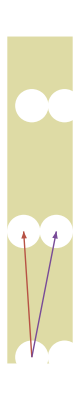

```mathematica
oppositeDecussateLattice:= Module[{},
lpts=Point[{{-1/8,0},{3/8,0},{-1/4,2},{1/4,2},{-1/8,4},{3/8,4}}];
g = Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{PointSize[0.06],White,lpts}
,{Thick,jParastichyColour[1],Arrow[{{-1/8,0},{-1/4,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{-1/8,0},{1/4,2}}]}

},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

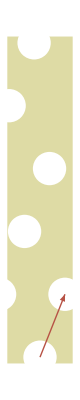
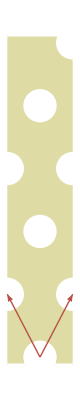
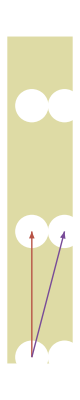
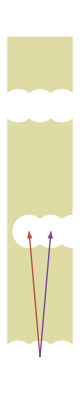
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Spiral | Alternate
distichous | Opposite
distichous | Decussate | Whorled
J=1 | J=1 | J=2 | J=2 | J=3
(0,1) | (0,1=1) | 2x(0,1,1) | 2x(0,1=1) | 3x(0,1,1)
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Txb0401LeafTypes=Ch3Types
```

```mathematica
txbExport[Txb0401LeafTypes];
```

```mathematica
Txb0401LeafTypes
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Spiral | Alternate
distichous | Opposite
distichous | Decussate | Whorled
J=1 | J=1 | J=2 | J=2 | J=3
(0,1) | (0,1=1) | 2x(0,1,1) | 2x(0,1=1) | 3x(0,1,1)
-Graphics- | -Graphics- | -Graphics- | oppositeDecussateLattice | -Graphics-

## Txb0403coordinates - figcoord

```mathematica
pointName[n_] := Subscript[ Style["l"<>,Italic,FontFamily->jStyle["FontFamily"]],Style[n,FontFamily->jStyle["FontFamily"]]];
```

```mathematica
Txb0403Coordinates:= Module[{lattice,d,h},
{d,h} = {0.4,0.1};
lattice= latticeCreateDH[{d,h},{-.5 h ,3.5 h}];
jpt[m_] := latticePoint[lattice,m];

cylinder:= {jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]};plotrange = {{-1.3,1.3},latticeGetCylinder[lattice][[2]]};latticep = latticePoints[ lattice];dashHeight = 2.5h;dash = Rotate[Line[{{-0.5,dashHeight-0.3 h},{-0.5,dashHeight+0.3 h}}], 60 Degree];doubledash = {dash,Translate[dash,{0,- 0.1 h}]};

dhshowpt =  jpt[2] - {1,0};pts = {White,Point[latticep],Translate[Point[latticep],{1,0}],Translate[Point[latticep],{-1,0}]};framerect = {FaceForm[LightGray],EdgeForm[None],Rectangle @@ Transpose@plotrange};glabel[x_] := Text[Style[x,FontFamily->jStyle["FontFamily"],FontSize->12],{plotrange[[1,1]],plotrange[[2,2]]},{-1,1},Background->White];

latexMath[text_,pos_,align_] := Text[Style[text,Italic,FontFamily->jStyle["FontFamily"]],pos,align];
divergenceRiseLabel={
 Text["divergence d",dhshowpt+{d/2,0},{0,2}]
, Text["rise h",dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]},{0,-1.2}]
,Arrowheads[.05]
, Arrow[{dhshowpt,dhshowpt+{latticeDivergence[lattice],0}}], Arrow[{dhshowpt+{latticeDivergence[lattice],0},dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]}}]
};
c2 = Graphics[
{
framerect,cylinder
,{PointSize[.02],pts}
,labelOffset={0,-2}; latexMath["(d,h)",jpt[1],labelOffset]
, latexMath["(2d-1,2h)",jpt[2],labelOffset]
, latexMath["(2d,2h)",jpt[2]+{1,0},labelOffset]
, latexMath["(3d-1,3h)",jpt[3],labelOffset]
,glabel["b"]
,Map[Text[#,{#,-.25 h}]&,{-1,-1/2,0,1/2,1}]
}
,PlotRange->plotrange,AspectRatio->1,Axes->True
,Ticks->{{},{{h,"h"}}}
,TicksStyle->FontFamily->jStyle["FontFamily" ]
,AxesOrigin->{0,0},AspectRatio->Full
,BaseStyle->{FontFamily->jStyle["FontFamily" ]}];

c3 =Graphics[
 {
framerect,cylinder
, doubledash, Translate[doubledash,{1,0}]
,{PointSize[.02],pts}
, Text[pointName[0],jpt[0],{0,1.4}]
, Text[pointName[1],jpt[1],{0,-1.4}]
, Text[pointName[2],jpt[2],{0,-1.4}]
, Text[pointName[3],jpt[3],{0,-1.4}]
,Arrowheads[.05]
, {Thick,jParastichyColour[1], Arrow[{jpt[0],jpt[1]}]}
, {Thick,jParastichyColour[2], Arrow[{jpt[0],jpt[2]}]}
, {Thick,jParastichyColour[3], Arrow[{jpt[0],jpt[3]}]}
, {Thick,Black, Line[{{0,0},{1/2,0}}]}
, {Thick,Black, Arrow[{{-1/2,0},{0,0}}]}
, {Thick,Black,Dotted, Arrow[{{1/2,0},{1,0}}]}
, {jParastichyColour[1],Text[pvectorName[1],jpt[1]/2,{-1.8,0}]}
, {jParastichyColour[2],Text[pvectorName[2],jpt[2]/2,{1.8,0}]}
, {jParastichyColour[3],Text[pvectorName[3],jpt[3]/2,{-1.8,0}]}
, {Black,Text[pvectorName[0],{1/3,0},{1,-1.4}]}
,glabel["c"]
},
PlotRange->plotrange,AspectRatio->1
];
c1= Graphics[
{
framerect,cylinder
,{PointSize[.05],pts}
,KeyValueMap[Style[Text[#1,#2],FontFamily->jStyle["DisplayFontFamily"]]&,lattice["namedLatticePoints"]]
,divergenceRiseLabel,
,latexMath["x",{plotrange[[1,2]],0},{1,-2}]
,latexMath["z",{0,plotrange[[2,2]]},{3,1}]
,glabel["a"]
}
,PlotRange->plotrange,AspectRatio->1,Axes->True
,Ticks->{{},{}}
,TicksStyle->FontFamily->jStyle["FontFamily" ]
,AxesOrigin->{0,0},AspectRatio->Full,AxesStyle->Arrowheads[{-0.0,0.05}]
,BaseStyle->{FontFamily->jStyle["FontFamily" ]}];


GraphicsRow[{c1,c2,c3},ImageSize->600,Frame->None]
];
```

```mathematica
(*txbExport@Txb0403Coordinates*)
```

## Txb0404Complementary vectors figcomplementary

```mathematica
complementary := Module[{lattice,spirh,psize,smidge,jpt,cylinder,cylinderminusone,latticep,latticeminusone,jplus1,gpoint,jminus1,bpoint},
	spirh = 2.5;
	psize= PointSize[.03];
	lattice= latticeCreateDH[{13/72,1},{-.4,spirh}];
	jpt[m_] := latticePoint[lattice,m];
	cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
	cylinderminusone = {Translate[cylinder,{-1,0}],Translate[cylinder,{1,0}]};
	
	latticep = latticePoints[ lattice];
	latticeminusone = Map[ {#[[1]]-1,#[[2]]} &, latticep];
	smidge = 0.00;
	jplus1 = jpt[2]+ {1,0};
	gpoint = jplus1 * ( 1/2 )/ (jplus1[[1]]);
	jminus1 = jpt[2]- {1,0};
	bpoint = jminus1 * ( -1/2 )/ (jminus1[[1]]);


Graphics[Style[
{
{jStyle["CylinderColour"],cylinder},{LightGray,cylinderminusone},
,{ jParastichyColour[1],Text[ pvectorName[2],0.75*jpt[2],{1.8,0}]}
,{ jParastichyColour[2],Text[ phatvectorName[2],0.75*(jpt[2]-{1,0}),{-1.8,0}]}
,{ Black,Text[ pvectorName[0],{-0.1,jpt[2][[2]]},{0,-1.8}]},
,{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[2]}+{smidge,smidge}]}
,{Thick,jParastichyColour[2],Line[{{0,0},bpoint}]}
,{Thick,jParastichyColour[2],Dashed,Translate[Line[{{0,0},bpoint}],{1,0}]}
,{Thick,jParastichyColour[3],Line[{{0,0},gpoint}]}
,{Thick,jParastichyColour[3],Dashed,Translate[Line[{{0,0},gpoint}],{-1,0}]}
,{Thick,jParastichyColour[3],Translate[Arrow[{gpoint,jplus1}],{-1,0}]}
,{Thick,jParastichyColour[3],Dashed,Translate[Line[{gpoint,jplus1}],{0,0}]}
,{Thick,jParastichyColour[2],Translate[Arrow[{bpoint,jminus1}],{1,0}]}
,{Thick,jParastichyColour[2],Dashed,Translate[Arrow[{bpoint,jminus1}],{0,0}]}
,{Thick,Black,Arrow[{jpt[2]-{1,0},jpt[2]}]}
,{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[2]}]}
,{White,psize,Point[latticep],Point[latticeminusone],Translate[Point[latticep],{1,0}]}
,Map[Style[Text[ paraGillNumber[#,0.03],jpt[#]] ,FontFamily->jStyle["DisplayFontFamily"]]&,{0,2}]
},jFont[16]],
PlotRange->{{-1.5,1.5},latticeGetCylinder[lattice][[2]]}
]
];
Txb0404Complementary:= complementary
```

## Txb0405Parastichy vector fig17725p

```mathematica
Txb0405Parastichy5 := Module[{lattice,jpt,pset,oset5},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,0.4}];
jpt[m_] := latticePoint[lattice,m];

pset[m_] := latticeParastichyLines[lattice,m];
oset5 = latticeParastichyLines[lattice,5,0];

Graphics[Style[{
	{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thin,jParastichyColour[2],pset[5]}
,{Thick,jParastichyColour[2],Arrow[{jpt[0],jpt[5]}]}
,{jParastichyColour[2],Text[pvectorName[5],jpt[5],{2,3}]}
,{White,PointSize[.03],Point[ latticePoints[ lattice]]}
,Map[Style[Text[ paraGillNumber[#,0.03],jpt[#]] ,FontFamily->jStyle["DisplayFontFamily"]]&,Range[-3,13]]
},jFont[Scaled[0.05]]],
PlotRange->{{-1/2,1/2},{-0.1,0.4}},PlotRangeClipping->True
]
];
```

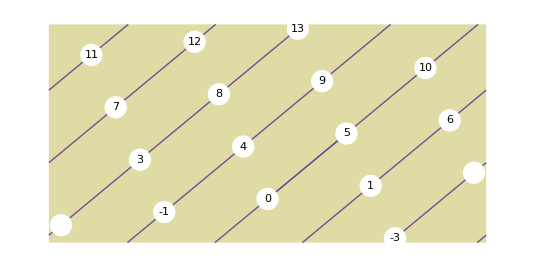

```mathematica
Txb0405Parastichy5//txbExport
```

## Txb0406Parastichy45 Parastichy lines fig1772

```mathematica
fig1772[paraList_] :=
Module[{lattice,cylinder,latticep},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,1.2}];
cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
latticep = latticePoints[ lattice];

jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];
pset[m_] := latticeParastichyLines[lattice,m];

Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
, Map[ {#[[1]],pset[#[[2]]] }&,paraList]
,{PointSize[.03],White,Point[latticep]}
},jFont[16]]
]
];

fig1772P0 := fig1772[{}];
fig1772P4 := fig1772[{{jParastichyColour[1],4}}];
fig1772P5 := fig1772[{{jParastichyColour[2],5}}];
fig1772P9 := fig1772[{{jParastichyColour[3],9}}];
```

```mathematica
notate1772[paraList_,doNotation_:True] :=
Module[{lattice,cylinder,latticep},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,1.2}];
cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
latticep = latticePoints[ lattice];

jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];
pset[m_] := latticeParastichyLines[lattice,m];
dhshowpt= jpt[25];
Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[doNotation,
{
 Arrow[{dhshowpt,dhshowpt+{latticeDivergence[lattice],0}}],
,Table[Text[ i,jpt[i],{0,1.4}],{i,0,10}]
, Text["divergence d",dhshowpt+{latticeDivergence[lattice]/2,0},{0,2}]
,
 Line[{dhshowpt+{latticeDivergence[lattice],0},dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]}}],
,Table[Text[ i,jpt[i],{0,1.4}],{i,0,10}]
, Text["rise h",dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]/2},{-2,0}]
}
]
, Map[ {#[[1]],pset[#[[2]]] }&,paraList]
,{PointSize[.03],White,Point[latticep]}
},jFont[16]]
]
];
```

```mathematica
sheffield1772 := notate1772[{}]
```

```mathematica
(*GraphicsGrid[{{
shExport[fig1772P0],
shExport[fig1772P4],
shExport[fig1772P5],
shExport[fig1772P9]
}}]*)
(* useful for powerpoint *)
```

```mathematica
Txb0406Parastichy45:= 
Show[fig1772[{{jParastichyColour[1],4},{jParastichyColour[2],5},{jParastichyColour[3],1}}],
Graphics[Style[{
 {Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[4]}]}
, {Thick,jParastichyColour[2],Arrow[{jpt[0],jpt[5]}]}
, {Thick,jParastichyColour[3],Arrow[{jpt[0],jpt[1]}]}
,{jParastichyColour[2],Text["5",jpt[5],{3,2.5}]}
,{jParastichyColour[1],Text["4",jpt[4],{-4,1}]}
,{jParastichyColour[3],Text["1",jpt[1],{7,1.5}]}
},jFont[16]]
],PlotRange->{{-1/2,1/2},{-0.1,.6}}
];
```

```mathematica
Txb0406Parastichy45//txbExport
```

-Graphics-

## Txb0407PPairs Parastichy pairs figplinesex

```mathematica
show0400PPairs := Module[{lattice},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,0.8}];
jpt[m_] := latticePoint[lattice,m];

cylinder := {jStyle["CylinderColour"],Rectangle[{-.5,cylinderLU[[1]]},{0.5,cylinderLU[[2]]}]};

(*pgram[m_,n_,through_] := parallelogram[{h,d},m,n,through];
*)
pset[m_] := latticeParastichyLines[lattice,m];
jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];


figplinesex057[m0_,m5_,m7_,through_] := Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thin,jParastichyColour[2],pset[m7]},{Thin,jParastichyColour[1],pset[m5]}
,{Thick,Black,Line[latticeParallelogram[lattice,m5,m7,through]]}
,{White,AbsolutePointSize[6],Point[latticePoints[lattice]]}
,Text[ ToString[m0],jpt[m0],{0,1.4}],
Text[ ToString[m5],jpt[m5],{-1,1.4}],
Text[ ToString[m7],jpt[m7],{0,-1.4}],
{Thick,jParastichyColour[1],Arrow[ {jpt[m0],jpt[m5]}]},
{Thick,jParastichyColour[2],Arrow[ {jpt[m0],jpt[m7]}]}
,
Style[Text[StringTemplate["(``,``)"][m5,m7], latticeLabelPosition[lattice],{-1,1},Background->White],FontSize->12]
},jFont[12]
]];

figplinesex57 = figplinesex057[0,5,7,13];
figplinesex38 = figplinesex057[0,3,8,9];
figplinesex59 =  figplinesex057[0,5,9,3];
figplinesex12:= Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
{Thin,jParastichyColour[1],pset[1]},
{White,AbsolutePointSize[6],Point[latticePoints[lattice]]},
Text[ "0",jpt[0],{0,1.4}],
Text[ "1",jpt[1],{-1,1.4}],
Text[ "2",jpt[2],{0,1.4}],
{Thick,jParastichyColour[1],Translate[Arrow[ {jpt[0],jpt[1]}],{ 0,-.01}]},
{Thick,jParastichyColour[2],Translate[Arrow[ {jpt[0],jpt[2]}],{0,.01}]},
{Thick,Black,Line[{jpt[12],jpt[13]}]},
Style[Text[StringTemplate["(``,``)"][1,2], latticeLabelPosition[lattice],{-1,1},Background->White],FontSize->12]
},jFont[12]
]];
GraphicsGrid[{{figplinesex59,figplinesex38},{figplinesex57,figplinesex12}},ImageSize->600]
];

Txb0407PPairs:= show0400PPairs
```

```mathematica
txbExport[Txb0407PPairs]
```

-Graphics-

## Txb0408Periodic

```mathematica
makec456 := Module[{lattice,jpt,cylinder,latticep,c4,c5,c6,framerect,plotrange},
lattice= latticeCreateDH[{0.4,0.08},{-.03,.6}];
jpt[m_] := latticePoint[lattice,m];
pset[m_] := latticeParastichyLines[lattice,m];

cylinder:= {jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]};
plotrange = {{-1.1,1.1},latticeGetCylinder[lattice][[2]]};
latticep = latticePoints[ lattice];
(*dashHeight = 2;
dash = Rotate[Line[{{-0.5,dashHeight-.1},{-0.5,dashHeight+.1}}], 30 Degree];
doubledash = {dash,Translate[dash,{0,-.05}]};

dhshowpt = 2;*)
pts = {Point[latticep],Translate[Point[latticep],{1,0}],Translate[Point[latticep],{-1,0}]};
framerect = {FaceForm[LightGray],EdgeForm[None],Rectangle @@ Transpose@plotrange};
glabel[x_] := Text[x,{plotrange[[1,1]],plotrange[[2,2]]},{-1,1},Background->White];


pn[n_] := latticeParastichyNumbers[lattice][[n]];
wps = 0.03;
ar = latticeGetCylinderLU[lattice][[2]]-latticeGetCylinderLU[lattice][[1]];
c4 =Graphics[Style[ {
framerect,cylinder
,{PointSize[wps],White,pts}
,Arrowheads[.04]
, {Thick,jParastichyColour[3], Arrow[{jpt[0],jpt[1]}]}
, {Thick,jParastichyColour[2], Arrow[{jpt[0],jpt[pn[1]]}]}
, {Thick,jParastichyColour[1], Arrow[{jpt[0],jpt[pn[2]]}]}
, {Thick,jParastichyColour[4], Arrow[{{0,0},{1,0}}]}
, {jParastichyColour[4],Text[pvectorName[0],{1/2,0},{-1,-1}]}
, {jParastichyColour[3],Text[pvectorName[1],jpt[1],{0,-1}]}
, {jParastichyColour[2],Text[pvectorName[pn[1]],jpt[pn[1]],{1.8,0}]}
, {jParastichyColour[1],Text[pvectorName[pn[2]],jpt[pn[2]],{-1.8,0}]}
},jFont[Scaled[0.05]]],
PlotRange->plotrange,AspectRatio->ar
];

c5 =Graphics[Style[ {
framerect,cylinder
,{jParastichyColour[2],Map[Translate[pset[ pn[1]],{#,0}]&,{-1,0,1}]}
,{jParastichyColour[1],Map[Translate[pset[ pn[2]],{#,0}]&,{-1,0,1}]}
, {jParastichyColour[3], Line[{jpt[0],jpt[1]}]}
, {jParastichyColour[4], Line[{jpt[0],{1,0}+jpt[0]}]}
,{PointSize[wps],White,pts}
},jFont[Scaled[0.03]]],
PlotRange->plotrange,AspectRatio->ar
];
c6 =Graphics[Style[ {
framerect,cylinder
,{jParastichyColour[4],Map[Translate[pset[ 0],{#,0}]&,{-1,0,1}]}
,{jParastichyColour[3],Map[Translate[pset[ 1],{#,0}]&,{-1,0,1}]}
, {jParastichyColour[2], Line[{jpt[0],jpt[pn[1]]}]}
, {jParastichyColour[1], Line[{jpt[0],jpt[pn[2]]}]}
,{PointSize[wps],White,pts}
},jFont[12]],
PlotRange->plotrange,AspectRatio->ar
];
{(*c4,*)c5,c6}
]

Txb0408Periodic:= GraphicsRow[makec456,Frame->None]
```

```mathematica
txbExport[Txb0408Periodic]
```

-Graphics-

## Txb0409apextriangle

```mathematica
Txb0409Apextriangle := Block[{m,n,u,v},
lattice= latticeCreateDH[{17/72,0.03},{-0.15,0.8}];
jpt[m_] := latticePoint[lattice,m];
pset[m_] := latticeParastichyLines[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];


pale = Background->Directive[Opacity[0.5],White];
tStyle[text_] := Style[text,Italic,FontFamily->jStyle["FontFamily"]];

Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice],
LightGray, Translate[latticeGraphicsCylinder[lattice],{1,0}]}
,
Text[ "(0,0)",jpt[0],{0,1.4},pale],
Text[ "(1,0)",{1,0},{0,1.4},pale],
apexpt = 4* jpt[5];
bpt = 4* jpt[4];
{Thin,jParastichyColour[2],pset[5],Translate[pset[5],{1,0}]},
{Thin,jParastichyColour[1],pset[4],Translate[pset[4],{1,0}]}
,Arrowheads[0.02]
,{Thick,Black,Arrow[ {{0,0},{1,0}}]},
{Thick,jParastichyColour[2],Arrow[ {{0,0},apexpt}]},
{Thick,jParastichyColour[2],Arrow[ {bpt,bpt+jpt[5]}]},
{Thick,jParastichyColour[1],Arrow[ {bpt+jpt[5],bpt+jpt[5]-jpt[4]}]},
{Thick,jParastichyColour[1],Arrow[ {{1,0},apexpt}]},
{Thick,Black,Arrow[ {bpt,bpt+jpt[1]}]},
{jParastichyColour[2],Text[tStyle@"up_n", bpt,{0,-3},pale]},
,{jParastichyColour[1],Text[tStyle@"vp_m",bpt+jpt[5],{-1.5,0},pale]}
,{Black,Text[ pvectorName[1], bpt,{-3,1},pale]}
,{jParastichyColour[1],Text[tStyle@"np_n",4*jpt[5]-2.5*jpt[4],{1,1},pale]}
,{jParastichyColour[2],Text[tStyle@"mp_n",2*jpt[5],{1.5,-0.5},pale]}
,{Black,
Text[tStyle@"p_0= mp_n - np_m"
,{0.5,0},{0,1.2}
,pale]}
},jFont[12]],AspectRatio->Automatic
]
];
```

```mathematica
txbExport[Txb0409Apextriangle]
```

-Graphics-

## Txb0410Generating interval plot

```mathematica
gLine[{m_,n_}] := gLine[{m,n,Missing[]}];
gLine[{m_,n_,hattedn__}] := Module[{gI,cI,bheight,gIrect,gIo,gIorect,u,v,umnv,umnvLines,res,iLine,Delta},
bheight = 0.1;
gI = If[MissingQ[hattedn],
generatingInterval[{m,n}],If[n==1,Interval[{0,1/2}], Interval[0,1/(2n)]
]
];
gIo = If[MissingQ[hattedn],
generatingOpposedInterval[{m,n}],If[n==1,Interval[{0,1/2}], Interval[0,1/(2n)]
]
];

gIrect  = {EdgeForm[None],FaceForm[LightGray],Rectangle[ {Min@gI,-bheight},{Max@gI,bheight}]};
gIorect  = {EdgeForm[None],FaceForm[jParastichyColour[1]],Rectangle[ {Min@gIo,-bheight},{Max@gIo,bheight}]};

iStyle =  euclideanDelta[{m,n}]<0;

iLine = {Thin,If[ iStyle,Dotted,Dashed],Line[ {{0,0},{1/2,0}}]};

tlabel = If[MissingQ[hattedn],StringTemplate["``,``"][m,n],StringTemplate["``,``"][m,hattedn]];


	res =
{
iLine
, gIrect
,gIorect 
,{Thin,Line[{{0,-bheight},{0,bheight}}],Line[{{1/2,-bheight},{1/2,bheight}}]}
, Text[ tlabel,{.55,0},{0,0}]
}
;
res];
```

```mathematica
(* reconsider with hats *)
```

```mathematica
Txb0410GeneratingIntervals := Graphics[Style[
{
MapIndexed[ Translate[gLine@  #1,{0,-First@#2}]&,{ {1,1},{1,2,"\!\(\*OverscriptBox[\(2\), \(^\)]\)"},{1,2},{2,3},{3,5},{5,8},{8,13},{13,21},{21,34},{1,3,"\!\(\*OverscriptBox[\(3\), \(^\)]\)"},{1,3},{3,4},{4,7},{7,11},{11,18},{18,29}}],
Line[{{0,0},{1/2,0}}]
,Text["0",{0,0},{-1,-1}]
,Text["divergence d",{1/4,0},{0,-1}]
,Text["1/2",{1/2,0},{0,-1}]
},
jFont[12]],
AspectRatio->1.5,PlotRange->{{0,.65},Automatic}];
```

```mathematica
Txb0410GeneratingIntervals
```

## Txb0411LatticesSpecialD

```mathematica
Txb0400ShowParastichyLines[h_,d_,cylinderLU_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
lattice = latticeCreateDH[{d,h},cylinderLU];
ll =latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];

latticePointSize = If[showCircle,Large,Small];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[lattice]/. Circle->Disk},Nothing[]],
, paraset
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]];
Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[Scaled[0.1]]]
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

```mathematica
Txb0411LatticesSpecialD := Module[{},
sPL[{h_,d_},label_] := Show[{
Txb0400ShowParastichyLines[h,d, {-0.1,2.1},True]
}];
GraphicsGrid[{{
(* label ignored and calculated direct *) 
sPL[{1.2,0},"(0,1)"],
sPL[{1,0},"(0=1,\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{0.8,0},"(1,0)"]
},{
sPL[{1.2,1/2},"(0,1=\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{Sqrt[3]/2,1/2},"(0=1=\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{0.6,1/2},"(1=\!\(\*OverscriptBox[\(1\), \(^\)]\),0)"],
sPL[{0.3,1/2},"(1=\!\(\*OverscriptBox[\(1\), \(^\)]\),2)"]
}
},ImageSize->600]
];
```

```mathematica
txbExport[Txb0411LatticesSpecialD]
```

-Graphics-

## Txb0412spiral

```mathematica
rName[n_] := Style[StringJoin["\!\(\*SubscriptBox[\(r\), \(",ToString[n],"\)]\)"],Italic,FontFamily->"Times"]
```

```mathematica
Txb0412Spiral := Module[{spirh,psize},
spirh = 1.5;
psize= AbsolutePointSize[2];
cylinderLU = {-.4,spirh};  

dospiral[{h_,d_},rList_] := Module[{nslope,pv,spiral,s1,s2,s3},
lattice = latticeCreateDH[{d,h},cylinderLU];
nslope[1] := (h/(h^2+d^2)){-h,d};
pv = Map[ latticeParastichyVectors[lattice],latticePrincipalParastichyPair[lattice]];

rPoints  =Association@Map[#->latticePoint[lattice,#]&,rList];
rText  =KeyValueMap[Text[rName[#1],If[#2[[1]]>0,#2-{1,0},#2],{1,-.5}]&,rPoints];
spiral = 
Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice],
LightGray,Translate[latticeGraphicsCylinder[lattice],{-1,0}]}
,{White,psize,Point[latticePoints[lattice]],
Translate[Point[latticePoints[lattice]],{-1,0}]}
,{Thin, Gray,Line[{1.4*nslope[1],-0.4  * nslope[1]}]}
,{Thick,jParastichyColour[1],Arrow[{{0,0},pv[[1]]}]},
,{Thick,jParastichyColour[2],Arrow[{{0,0},pv[[2]]}]}
,{Black,rText}
},jFont[12]
],AspectRatio->Automatic];

spiral
];

s1 = dospiral[{0.08,7/72},{}];
s2 = dospiral[{ .115, 7/72},{3,4,5,6,7}];
s3 = dospiral[{ 0.4, 7/72},{}];
GraphicsGrid[ {{s3,s2,s1}},ImageSize->600]
];
```

## Txb0413 SpiralExample

```mathematica
addSubTree[mnpairs_] := DeleteDuplicates@Flatten[Map[ {#,{#⟦1⟧,#⟦1⟧+#⟦2⟧},{#⟦2⟧,#⟦1⟧+#⟦2⟧}}&,mnpairs],1];


panelLabel [{m_,n_},at_,scaling_:0.08] := Module[{textsize,obj},
textsize[{x_,y_}] := Scaled[scaling * Min[Sqrt[y],0.5]];
obj=Grid[
{{Style[StringTemplate["``,``"][m,n],jFont[textsize[at]]]}}
,Frame->None
];
Inset[obj,at]
];

spiralTreePlot[mnPairs_,labelPairs_,opts:OptionsPattern[]] := Module[{regionLabel,prunedTree},
regionLabel[mn_] := panelLabel[mn,vanItersonLabelPoint[mn],0.15];

prunedTree = {
Map[{LightGray,vanItersonTouchingCirclePrimary[#]}&,mnPairs]
,{LightGray,Map[vanItersonTouchingCircleNonPrimary,mnPairs]}
 };


Graphics[
{
 prunedTree
,Map[regionLabel,labelPairs]
},
Evaluate[FilterRules[{opts}, Options[Graphics]]]
]
];
```

```mathematica
makespiralBackground :=  Module[{mnPairs,labelPairs,tplaces,ticks},
mnPairs = Join[Nest[addSubTree,{{1,2}},6],{{0,1}}];
labelPairs = Join[Nest[addSubTree,{{1,0}},3],{{1,4}},{}];

spiralRegions = Map[colourSpiral,{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}];
Show[
Graphics@spiralRegions,
spiralTreePlot[ mnPairs,{},PlotRange->
{{0.,1/2},{0,0.5}}
,Axes->True,Ticks->{{0,1/2},{0,1/2}},
AxesLabel->{"d","h"}
,PlotRangeClipping->True
 ,BaseStyle->  {FontFamily->  jStyle["FontFamily"]}
]
]
];

hatTransition[n_] := {Red,Circle[{  1/(2 n+1),0},1/(2 n+1)]}
hdofTransition[d_,n_]:= {d,Module[{z=1/(2n+1)}, Sqrt[ z^2- (d- z)^2]]};
```

```mathematica
croppedPoly[mn_,a_,b_] := Module[{intersection,poly},
poly=vanItersonPolygon[mn,b];
intersection= RegionIntersection[poly,Rectangle[{0,0},{1/(2*Last[mn]),1}]];
If[Head[intersection]==BooleanRegion,
	intersection=DiscretizeRegion[intersection]];
intersection
];
```

```mathematica
rColours["01","Plus"] = ColorData[50,1];
rColours["01","Minus"] = ColorData[50,2];
rColours["10","Plus"] =  ColorData[50,7];
rColours["10","Plus",1] =  ColorData[50,7];
rColours["10","Plus",-1] =  ColorData[50,5];
rColours["10","Minus"] =  ColorData[50,4];
colourSpiral[mn_] := {
{rColours["10","Plus"],croppedPoly[mn,"Ordered","Plus"]}
,{rColours["10","Minus"],croppedPoly[mn,"Ordered","Minus"]}
}
twoLabel[{d_,h_}] := Module[{slattice,lpnx,hats},
slattice =  latticeCreateDH[{d,h},{0,2}];
lpn = Take[latticeParastichyNumbers[slattice],2]/. (Private`hat)->hat;
hats = Map[hatName,lpn];
hats = Riffle[hats,","];
hatDisplay = DisplayForm@RowBox[hats];
hatDisplay
];
threeLabel[{d_,h_}] := Module[{slattice,lpn,hats},
slattice =  latticeCreateDH[{d,h},{0,2}];
lpn = latticeParastichyNumbers[slattice]/. (Private`hat)->hat;
hats = Map[hatName,lpn];
hatDisplay = DisplayForm@RowBox[hats];
hatDisplay
];
spiralBackground= makespiralBackground;
Txb0413SpiralExample := viSpirals2
```

```mathematica
txbExport[Txb0413SpiralExample]
```

-Graphics-

```mathematica
viSpirals2 :=  Module[{kList},
kList = {2,3,4};

Show[
spiralBackground,
Graphics[Map[viTwoLattice,kList]]
,PlotRange->{{0,0.5},{0,0.5}}
,Ticks -> {{0,1/8,1/6,1/4,1/2},{0,1/2}}
,Axes->True,BaseStyle->Directive[FontFamily->jStyle["FontFamily"]]
,AxesLabel-> {"d","h"}
]
];


viTwoLattice[k_] := Module[{d,hd,labels,lpn},
d = Mean@{1/(2(k+1)),1/(2k)};
(*hd = Echo@dhColumnTwo[d,k];
*)
hd1 = {{0.3,0.45},{0.3,0.234},{0.145,0.234},{0.22,0.1597},{0.1125,0.1597}
,{0.15,0.12},{0.09,0.12}};

labels = Map[ Text[ twoLabel[#],#,Background->White]&,hd1];
{
labels
}
];

hatName[n_] := Style[ToString[n],FontFamily->jStyle["FontFamily"]];
hatName[hat[n_]] := DisplayForm[OverHat[hatName[n]]]
```

## Txb0414Reduction figreduction

```mathematica
Txb0414Reduction := Module[{smidge=0.01,spirh,h,d,lattice,jpt,nslope},
spirh = .5;h = .03;d = 17/72;cylinderLU = {-0.1,spirh};  
lattice = latticeCreateDH[{d,h},cylinderLU];

jpt[m_] := latticePoint[lattice,m];

nslope[5] = { - jpt[5][[2]],jpt[5][[1]] };

Graphics[
Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
Arrowheads[jStyle["ArrowheadSpec"]]
,{White,Point@latticePoints[lattice]}
, { jParastichyColour[1],Text[ pvectorName[5],jpt[5],{-2,0}]}
,{ jParastichyColour[2],Text[ pvectorName[14],jpt[14],{1,-1.5}]}
,{ jParastichyColour[3],Text[ pvectorName[4],jpt[12],{1,-1.5}]}
,{jParastichyColour[1],Translate[Arrow[{{0,0},jpt[5]}],{0,0}]}
,{jParastichyColour[2],Translate[Arrow[{{0,0},jpt[14]}],{0,0}]}
,{jParastichyColour[3],Translate[Arrow[{jpt[8],jpt[12]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[9]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[9]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[4]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[-1]}],{0,0}]}
,{
FaceForm[None],EdgeForm[Black],
Translate[Rotate[Scale[Rectangle[],0.02,{0,0}],ArcTan@@nslope[5]+π/2,{0,0}],nslope[5]*0.55]
}
,{Thin,Dashed,Black,Line[{ nslope[5]*-1.2,nslope[5]*0.7}]}
,{Thin,Dashed,Red,Line[{ jpt[-6],jpt[19]}]}
,Text["p_14- p_5",jpt[9],{1,-1.5}]
,Text["p_14- 2 p_5",jpt[4],{1,-1.5},Background->jStyle["CylinderColour"]]
,Text["p_14- 3p_5",jpt[-1],{1,-1.5}]
}
,jFont[Scaled[0.03]]],
PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

## Txb0415SumDifference Turing Fundamental theorem - figsumdiff

```mathematica
Txb0415SumDifference :=  Module[{},
lattice= latticeCreateDH[{17/72,0.03},{-.08,.34}];
jpt[m_] := latticePoint[lattice,m];
paraNormal[n_] := Module[{x,z},{x,z}=jpt[n]; (z/(x^2+z^2)){-z,x}];
{pp1,pp2,pp3} = latticePrincipal3ParastichyNumbers[lattice];
pp4 = If[pp3==pp1+pp2, Abs[pp2-pp1],pp1+pp2];
Graphics[Style[
{
{jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]}
,{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[pp1]}]}
,{Thick,jParastichyColour[2],Arrow[{jpt[0],jpt[pp2]}]}
,{Thin,jParastichyColour[4],Arrow[{jpt[0],jpt[pp4]}]}
,{Thin,jParastichyColour[3],Arrow[{jpt[0],jpt[pp3]}]}
,{Thin,jParastichyColour[1],Line[{jpt[pp2-2 pp1],jpt[pp2+3pp1]}]}
,{Thick, Gray, Line[ {jpt[0]-0.4paraNormal[pp1],jpt[0] +  0.4 paraNormal[pp1]}]}
,{Text[paraNumber[pp1],jpt[pp1],{3,0}]}
,{Text[paraNumber@pp2,jpt[pp2],{-3,0}]}
,{Text[paraNumber@pp4,jpt[pp4],{-3,0}]}
,{Text[paraNumber@pp3,jpt[pp3],{-3,0}]}
,{AbsolutePointSize[6],White, latticeGraphicPoints[lattice]}
}],PlotRange->latticeGetCylinder[lattice]
,ImageSize->600
]
];
```

## Txb0416Fiblatt Fibonacci lattices Txb0400FibLattice

```mathematica
showFibParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = latticeLabel[lattice];
aline[ix_] := { jParastichyColour[ix],
Line[{latticePoint[lattice,0],latticeVector[lattice,First@ll[[ix]]]}]};arrows = Table[{aline[ix],Dashed,Translate[aline[ix],{-1,0}]},{ix,Length[ll]}];labels = MapIndexed[Style[Text[#1,latticeVector[lattice,#1],If[#1===1,Offset[{0,-1}],Offset[{0,0}]],Background->jStyle["CylinderColour"]] ,jParastichyColour@First[#2],jFont[12]]&,ll,{2}];latticePointSize = If[showCircle,Large,Small];labels = Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]];Graphics[{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},{Thick,arrows},{PointSize[Medium],White,Point[latticePoints[lattice]]},labels},PlotRange->latticeGraphicsPlotRange[lattice],ImageSize->150]];

f[h_] := showFibParastichyLines[latticeCreateDH[{GoldenRatio-1,h},{-0.01,
If[h>= 0.2,1.45,0.45]}]];

Txb0416FibLattices := Grid[Map[f,{{1,0.5,0.2},{0.15,0.1,0.05},{0.04,0.025,0.015}},{2}]];
```

```mathematica
txbExport@Txb0416FibLattices
```

-Graphics-

## Txb0417LatticeTypes Lattices organised by length Txb0400LatticeTypes

```mathematica
showLatticeParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
arrows = MapIndexed[{ jParastichyColour@First[#2],Arrow[{latticePoint[lattice,0],latticeVector[lattice,#1]}]}&,ll,{2}];paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];paraset ={LightGray,llines};latticePointSize = If[showCircle,0.01,Small];latticeP= latticeSetCylinderLU[lattice,{-0.4,0.8}];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[latticeP]/. Circle->Disk},Nothing[]],
,{Thin, paraset}
,{Thick,arrows}
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]],
Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];

figShowHex25 := showLatticeParastichyLines[latticeHexagonal[{2,5},{-0.2,0.6}]];
figShowTC25 := showLatticeParastichyLines[latticeTouchingCircle[{2,5},{-0.2,0.6}]];
figShowMN23 := showLatticeParastichyLines[latticeWithMN[{2,3},{-0.2,0.6}]];
figShowMN25 := showLatticeParastichyLines[latticeWithMN[{2,5},{-0.2,0.6}]];

(* viTouchingCircleBranch[{2,3}] *)
b[theta_] := {1/5,0} + (1/5) * {Cos[theta],Sin[theta]}
```

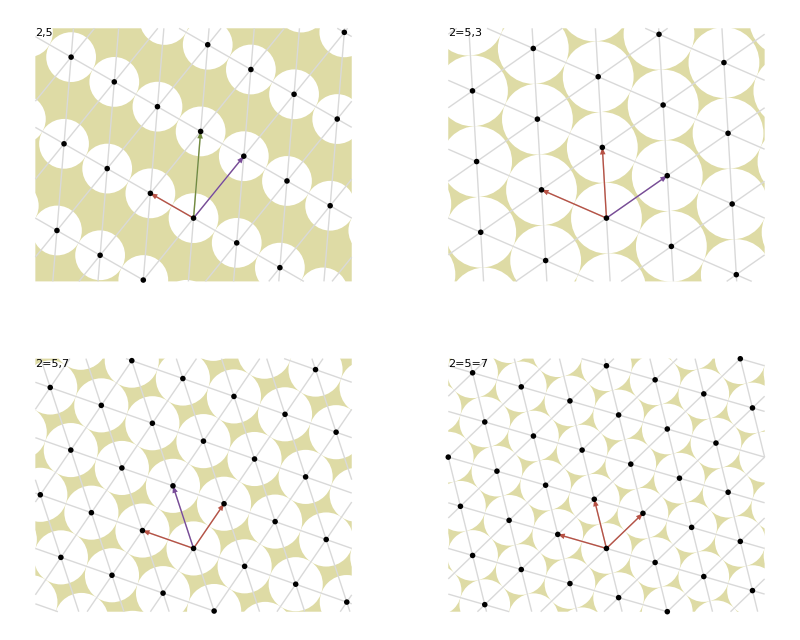

```mathematica
Txb0417LatticeTypes
```

```mathematica
figShowNoli25 := Module[{},
{nolic,nolir,nolia} = List@@vanItersonTouchingCirclePrimaryNonOpposed[{2,5}];
nolim = Mean[nolia];
dhNoli = nolic + nolir * {Cos[nolim],Sin[nolim]};
(Off[Greater::meprec];Off[LessEqual::meprec];
showLatticeParastichyLines[latticeCreateDH[dhNoli,{-0.2,0.6}]])
];
(* touching circle oddness *)

 Txb0417LatticeTypes := GraphicsGrid[{{figShowMN25,figShowNoli25},{figShowTC25,figShowHex25}}]
```

```mathematica
txbExport[Txb0417LatticeTypes]
```

-Graphics-

```mathematica
OxOppo := Module[{},
{oppo41 =showLatticeParastichyLines[
latticeCreateDH[latticeDHNonOpposedTC[{1,4}],{-0.2,0.8}]]
,
nonOppo41 =showLatticeParastichyLines[
latticeCreateDH[{0.24,0.06},{-0.2,0.8}]
]
};
GraphicsRow[{nonOppo41,oppo41}]
];
```

```mathematica
txbExport[OxOppo]
```

```mathematica
CamOppo := Module[{},
{oppo41 =showCamLatticeParastichyLines[
latticeCreateDH[latticeDHNonOpposedTC[{1,4}],{-0.2,0.8}]]
,
nonOppo41 =showCamLatticeParastichyLines[
latticeCreateDH[{0.24,0.06},{-0.2,0.8}]
]
};
GraphicsRow[{nonOppo41,oppo41}]
];
```

```mathematica
showCamLatticeParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = Echo@latticeLabel[lattice];
ll= {{1,4}};
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
arrows = MapIndexed[
{ jParastichyColour@First[#2],
Arrow[{latticePoint[lattice,0],latticeVector[lattice,#1]}]}&,ll,{2}];

paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];
paraset ={LightGray,llines};
latticePointSize = If[showCircle,Large,Small];

latticeP= latticeSetCylinderLU[lattice,{-0.4,0.8}];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[latticeP]/. Circle->Disk},Nothing[]],
,{Thin, paraset}
,{Thick,arrows}
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]]
(*,Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
*)
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

## Txb0418loworder

```mathematica
Txb0400ShowLattice[lattice_]  :=  Module[{ll,llines,paraset,g},

ll = latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];

g=Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,
{FaceForm[White],EdgeForm[None],latticeCircles[lattice] /. Circle->Disk},
paraset
,Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
(*,{Point[lattice]}
*)},PlotRange->latticeGraphicsPlotRange[lattice]
];
g
];
```

```mathematica
Txb0418LowOrder := Module[{},
	cylinderLU = {0,1.2};
	p0e1e1 = latticeHexagonal[{0,1},cylinderLU];
	p2e1 = latticeOrthogonal[{1,1},cylinderLU];
	g1 = Txb0400ShowLattice/@{p0e1e1,p2e1};
cylinderLU = {0,0.8};
p1e1 = latticeTouchingCircle[{1,1},cylinderLU];
p1e2= latticeOrthogonal[{1,2},cylinderLU];
p1e2e3 = latticeHexagonal[{1,2},cylinderLU];
g2 = Txb0400ShowLattice/@{p1e1,p1e2,p1e2e3};
cylinderLU = {0,.6};
p2e3 = latticeOrthogonal[{2,3},cylinderLU];
p2e3e5 = latticeHexagonal[{2,3},cylinderLU];
p3e5= latticeOrthogonal[{3,5},cylinderLU];
p3e5e8 = latticeHexagonal[{3,5},cylinderLU];
g3 = Txb0400ShowLattice/@{p2e3,p2e3e5,p3e5,p3e5e8};
cylinderLU = {0,.4};
p3e8 = latticeOrthogonal[{3,8},cylinderLU];
p5e8e13 = latticeHexagonal[{5,8},cylinderLU];
cylinderLU = {0,.8};
p1e3 = latticeHexagonal[{1,3},cylinderLU];
p1e3o = latticeOrthogonal[{1,3},cylinderLU];
g4 = Txb0400ShowLattice/@{p3e8,p5e8e13,p1e3,p1e3o};
cylinderLU = {0,.6};
	p1e3e4 = latticeTouchingCircle[{1,3},cylinderLU];
p3e4  = latticeOrthogonal[{3,4},cylinderLU];
p1e5 = latticeTouchingCircle[{3,4},cylinderLU];
p2e5 = latticeTouchingCircle[{2,5},cylinderLU];
g5 =Txb0400ShowLattice/@{p1e3e4,p3e4,p1e5,p2e5};
g = figLowOrder = Row[{Column[g1],Column[g2],Column[g3],Column[g4],Column[g5]},Spacer[1],Frame->False,Alignment->Center];
g
];
```

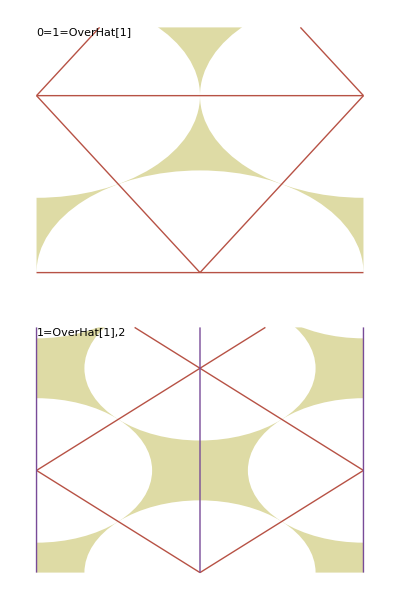
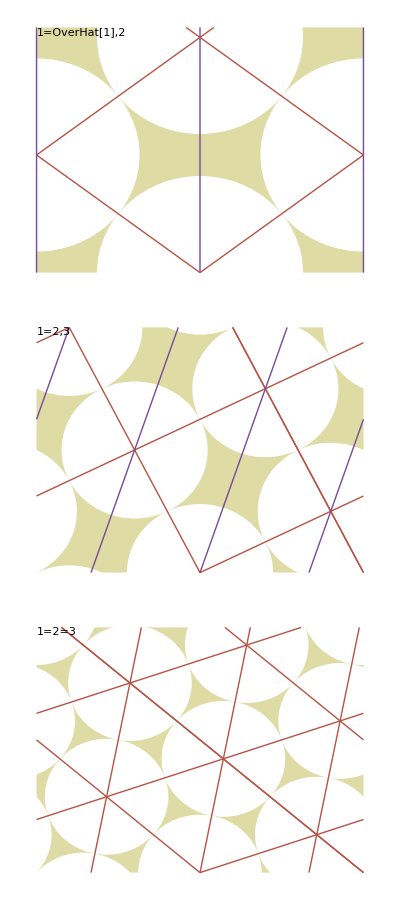
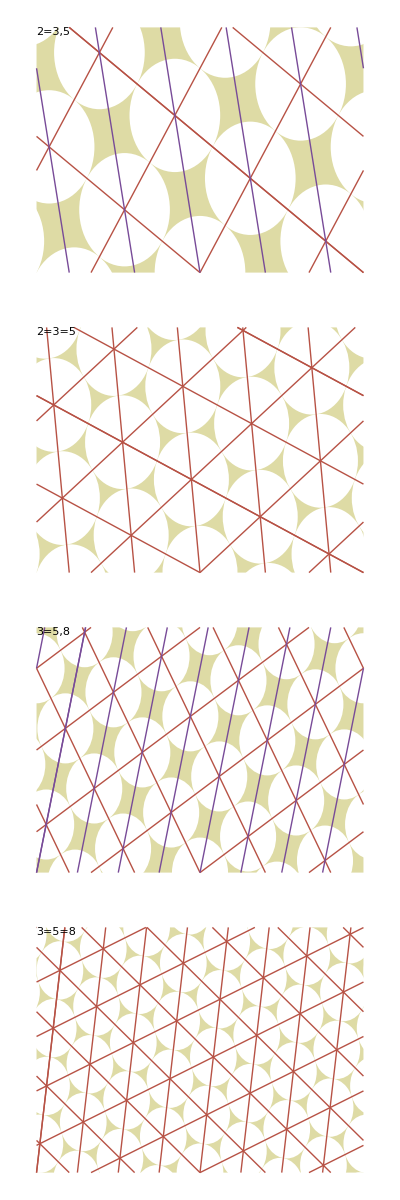
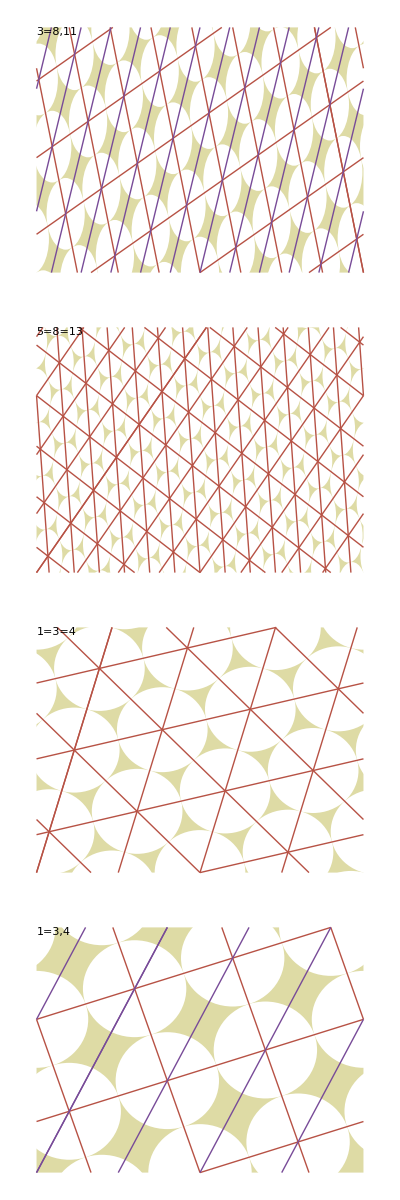
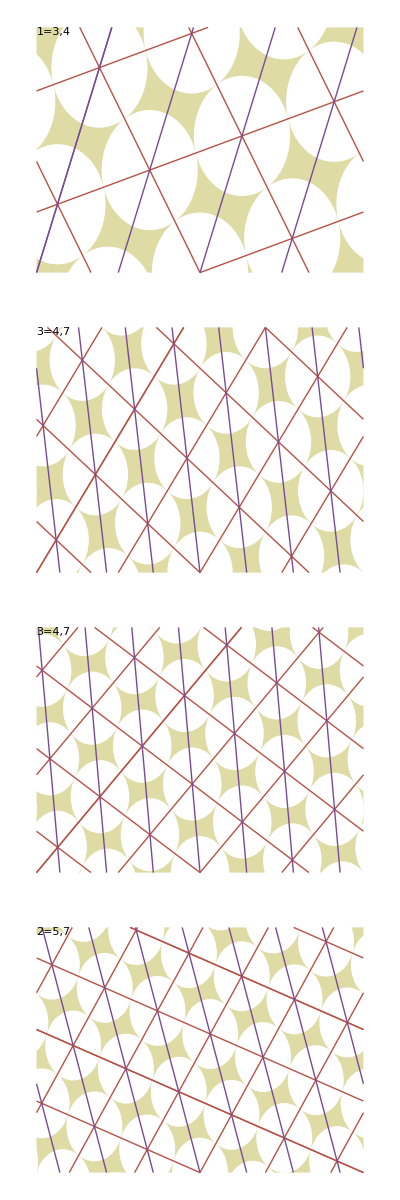

```mathematica
txbExport[Txb0418LowOrder]
```

## Txb0419JeanX figcounterx

```mathematica
Txb0419JeanX := Graphics@Module[{smidge,h,d,spirh,cylinderLU,lattice,jpt,pLine},
h = .1;d = 7/72;spirh = .5;
cylinderLU = {-0.1 * spirh ,spirh};  
lattice = latticeCreateDH[{d,h},cylinderLU];
jpt[m_] := latticePoint[lattice,m];
smidge = 0.02;
pLine = latticeParastichyLines[lattice,1];
pLine = {pLine,Translate[pLine,{-1,0}]};

spiral = 
Graphics[Style[
{
Arrowheads[.02],
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
{LightGray,Translate[latticeGraphicsCylinder[lattice],{-1,0}]}
,{Thin,Red,pLine}
,{
{White,Point[latticePoints[lattice]],
Translate[Point[latticePoints[lattice]],{-1,0}]}}

,{ jParastichyColour[2],Text[ pvectorName[2],jpt[2],{2,0}]}
,{ jParastichyColour[1],Text[ pvectorName[1],jpt[1],{2,0}]}
,{ jParastichyColour[2],Text[ phatvectorName[2],jpt[2]-{1,0},{2,0}]}
,Translate[{Thick,jParastichyColour[2],Arrow[{{0,0},jpt[2]}]},{smidge,0}]
,Translate[{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[1]}]},{-smidge,0}]
,{Thick,jParastichyColour[2],Dashed,Arrow[{{0,0},jpt[2]- {1,0}}]}
},jFont[16]],AspectRatio->Automatic
];
spiral
];
```

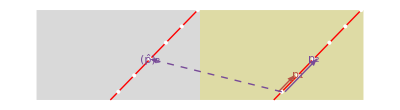

```mathematica
txbExport[Txb0419JeanX]
```

## Txb0420Multijugacy

```mathematica
shoMultiJugate := Module[{d,h,spirh,cylinderLU,lattice,latticeJ,smidge,jpt},
d = .2;h = .1;spirh = 10 h ;cylinderLU = {-0.1 * spirh ,spirh};  
lattice = latticeCreateDH[{d,h},cylinderLU];
latticeJ = latticeCreateDH[{d,h,2},cylinderLU];
smidge=0.1;
jpt[m_] := latticePoint[lattice,m];
Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},{jStyle["CylinderColour"],Translate[latticeGraphicsCylinder[latticeJ],{1+smidge,0}]}
,{
{White,Point[latticePoints[lattice]],
Translate[Point[latticePoints[latticeJ]],{1+smidge,0}]}}
,Translate[{Thick,jParastichyColour[2],Arrow[{{0,0},jpt[4]}]},{0,0}]
,Translate[{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[1]}]},{0,0}]
,Translate[{Thick,jParastichyColour[2],Arrow[{{0,0},jpt[4]/2}]},{1+smidge,0}],Translate[{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[1]/2}]},{1+smidge,0}]}]
];
Txb0420MultiJugate:= shoMultiJugate;
```

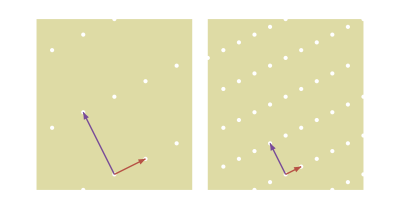

```mathematica
txbExport@Txb0420MultiJugate
```

## Oneonehat bonnet

```mathematica
(*
PersistentSymbol["persistentTextbookFigureDirectory","Local"]="C:\\Users\\jonat\\Documents\\GitHub\\MathematicalPhyllotaxis\\LaTeX\\Figures"
bonnetImage = Import[PersistentSymbol["persistentTextbookFigureDirectory","Local"],"BonnetXXCropThirdOrder.jpg"];
*)
bonnetImage = Import[FileNameJoin[{PersistentSymbol["persistentTextbookFigureDirectory","Local"],"BonnetXXCropThirdOrder.jpg"}]];

Txb0400duBonnet := Module[{lattice,jpt},
lattice= latticeCreateDH[{1/2,0.6},{-0.4,2.2}];
jpt[m_] := latticePoint[lattice,m];
jpt[hat[m_]] := latticePoint[lattice,m,False];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.03],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]},
{jParastichyColour[1],Text[pvectorName[1],(jpt[0]+jpt[1])/2,{-2,0}]},
{jParastichyColour[1],Text[phatvectorName[1],(jpt[0]+jpt[hat[1]])/2,{2,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[hat[1]]}]}
},jFont[Scaled[0.03]]]
}
,{Inset[bonnetImage,{0.8,-0.4},{Left,Bottom},{Automatic,2.6}]}
},
PlotRange->{{-1,2},{-0.5,2.5}},Axes->False
]
];
```

Import::nffil: File C:\Users\jonat\Documents\GitHub\MathematicalPhyllotaxis\LaTeX\Figures\BonnetXXCropThirdOrder.jpg not found during Import.

```mathematica
shExport[Txb0400duBonnet]
```

## Sheffield movie

```mathematica
frameFibParastichyLines[lattice_,showCircle_:True]  :=  Module[{ll,aline,arrows,labels,latticePointSize},
ll = latticeLabel[lattice];
aline[ix_] := { jParastichyColour[ix],
Line[{latticePoint[lattice,0],latticeVector[lattice,First@ll[[ix]]]}]};
arrows = Table[{aline[ix],Dashed,Translate[aline[ix],{-1,0}]},{ix,Length[ll]}];

latticePointSize = If[showCircle,Large,Small];
labels = Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]];
Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thick,arrows}
,{PointSize[Medium],White,Point[latticePoints[lattice]]}
,labels
(*,{PointSize[Medium],Black,Point[latticePoint[lattice,1]]}
*)},PlotRange->latticeGraphicsPlotRange[lattice],
ImageSize->300
]
];
sToh[s_] := Module[{t}, t= If[s<1/2,2s,2-2 s ];Exp[  ( t+1/2) Log [0.015]]];
frameFib[s_,seconds_] := frameFibParastichyLines[
latticeCreateDH[{GoldenRatio-1, sToh[s/seconds]},{-0.01,1.45}]];
```

```mathematica
sheffieldFibShow := Module[{vf},
vf = VideoGenerator[frameFib[#,10]&,10];
CopyFile[FindFile@Information[vf,"ResourcePath"]
,"SheffieldFib.mp4",OverwriteTarget->True]
];
```

```mathematica
(*
sheffieldFibShow
*)
```

## Ordinary pairs not currently used

```mathematica
cylinderLU = {-0.1,2.1};
cylinder2 =  {-0.1,0.2};
dOrdinary = N[17/72];

soPL[{h_,d_},cyl_,showCircle_:True] := Txb0400ShowParastichyLines[h,d,cyl,showCircle];

figordinaryA := GraphicsGrid[{{
soPL[{1.2,dOrdinary},cylinderLU,True]
,soPL[{0.8,dOrdinary},cylinderLU,True]
,soPL[{0.6,dOrdinary},cylinderLU,True]
,soPL[{0.3,dOrdinary},cylinderLU,True]
},{
soPL[{0.15,dOrdinary},cylinderLU,True]
,soPL[{0.1,dOrdinary},cylinderLU,True]
,soPL[{0.05,dOrdinary},cylinderLU,True]
,soPL[{0.025,dOrdinary},cylinderLU,True]
}
},ImageSize->600];
```

```mathematica
Bshow= True;
figordinaryB := GraphicsGrid[{
{
 soPL[{0.025,dOrdinary},cylinder2,Bshow]
,soPL[{0.015,dOrdinary},cylinder2,Bshow]
,soPL[{0.01,dOrdinary},cylinder2,Bshow]

},{
soPL[{0.005,dOrdinary},cylinder2,Bshow]
,soPL[{0.002,dOrdinary},cylinder2,Bshow]
,soPL[{0.001,dOrdinary},cylinder2,Bshow]
}
},ImageSize->600];
```